## Práctica 2 - Función característica

## La distribución normal

Función característica de la normal estándar

```mathematica
fcnorm[t_]=CharacteristicFunction[NormalDistribution[],t]
```

ⅇ^(-t^2/2)

```mathematica
FourierTransform[PDF[NormalDistribution[],x],x,t,FourierParameters->{1,1}]
```

ⅇ^(-t^2/2)

```mathematica
Integrate[Exp[ⅈ t x]PDF[NormalDistribution[],x],{x,-∞,∞}]
```

ⅇ^(-t^2/2)

```mathematica
Expectation[Exp[ⅈ t x],x\[Distributed]NormalDistribution[]]
```

ⅇ^(-t^2/2)

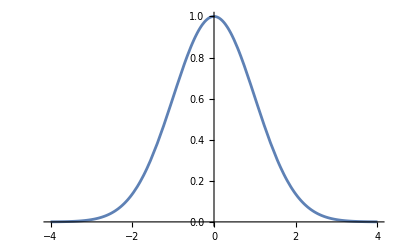

```mathematica
Plot[fcnorm[t],{t,-4,4}]
```

Fórmula de inversión para densidades. Los parámetros de Fourier según la fórmula empleada por Mathematica deben ser  (ver documentación)

```mathematica
InverseFourierTransform[fcnorm[t],FourierParameters->{1,1},t,x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
PDF[NormalDistribution[],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

Normal no estándar

```mathematica
dnormnostd[μ_,σ_]=TransformedDistribution[σ x+μ,x\[Distributed]NormalDistribution[],Assumptions->σ>0];
```

```mathematica
fcnormnostd[t_,μ_,σ_]=CharacteristicFunction[dnormnostd[μ,σ],t]
```

ⅇ^(ⅈ t μ-(t^2 σ^2)/2)

```mathematica
Re[fcnormnostd[t,μ,σ]]//ComplexExpand
```

ⅇ^(-1/2 t^2 σ^2) Cos[t μ]

```mathematica
Im[fcnormnostd[t,μ,σ]]//ComplexExpand
```

ⅇ^(-1/2 t^2 σ^2) Sin[t μ]

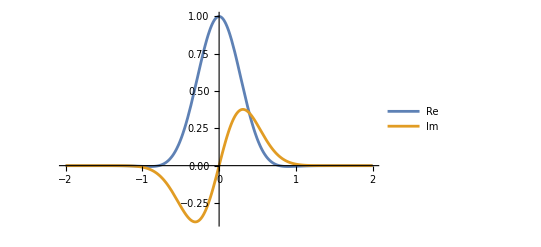

```mathematica
Plot[{Re[fcnormnostd[t,2,3]],Im[fcnormnostd[t,2,3]]},{t,-2,2},PlotRange->All,PlotLegends->{Re,Im}]
```

```mathematica
ParametricPlot3D[{t,Re[fcnormnostd[t,2,3]],Im[fcnormnostd[t,2,3]]},{t,-1,1},AxesLabel->{t,Re,Im}]
```

-Graphics3D-

### Comprobación experimental de cotas

Cota para distancias:

```mathematica
cotad[t_,s_]=2(1-Re[fcnorm[t-s]])
```

2 (1-Re[ⅇ^(-1/2 (-s+t)^2)])

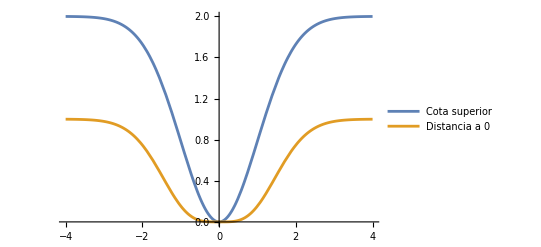

```mathematica
Plot[{cotad[t,0],Abs[fcnorm[t]-1]^2},{t,-4,4},PlotLegends->{"Cota superior","Distancia a 0"}]
```

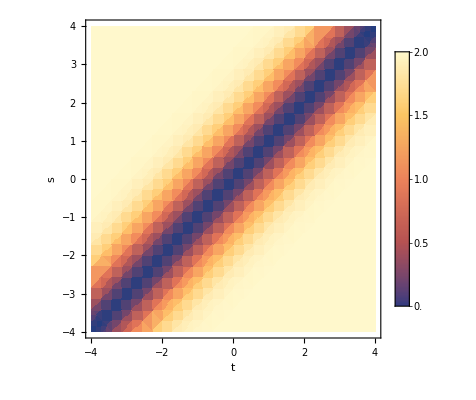

```mathematica
DensityPlot[cotad[t,s],{t,-4,4},{s,-4,4},Axes->True,AxesLabel->Automatic,PlotLegends->Automatic]
```

Cota para la medida de la cola de la distribución:

```mathematica
cotac[r_]=r/2 Integrate[1-fcnorm[t],{t,-2/r,2/r}]
```

1/2 r (4/r-√(2 π) Erf[(√2)/r])

```mathematica
probcola[r_]=Probability[Abs[x]>r,x\[Distributed]NormalDistribution[],Assumptions->r>0]
```

Erfc[r/(√2)]

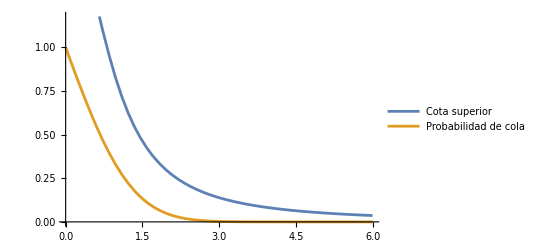

```mathematica
Plot[{cotac[r],probcola[r]},{r,0,6},PlotLegends->{"Cota superior","Probabilidad de cola"}]
```

### Momentos y cumulantes

Serie de Taylor de  hasta orden 4

```mathematica
Series[fcnorm[t],{t,0,4}]
```

1-t^2/2+t^4/8+O[t]^5

Momentos hasta de orden 4 de  como coeficiente correspondiente de la serie de Taylor de

```mathematica
Table[(n!)/ⅈ^n SeriesCoefficient[fcnormnostd[t,μ,σ],{t,0,n}],{n,1,4}]//Simplify
```

{μ,μ^2+σ^2,μ^3+3 μ σ^2,μ^4+6 μ^2 σ^2+3 σ^4}

```mathematica
Table[1/ⅈ^n D[fcnormnostd[t,μ,σ],{t,n}]/.t->0,{n,1,4}]//Simplify
```

{μ,μ^2+σ^2,μ^3+3 μ σ^2,μ^4+6 μ^2 σ^2+3 σ^4}

```mathematica
D[fcnormnostd[t,μ,σ],{t,2}]/.t->0
```

-μ^2-σ^2

```mathematica
2!SeriesCoefficient[fcnormnostd[t,μ,σ],{t,0,2}]
```

-μ^2-σ^2

Primeros 8 cumulantes de

```mathematica
Table[Cumulant[dnormnostd[μ,σ],n],{n,1,8}]
```

{μ,σ^2,0,0,0,0,0,0}

## Teorema de continuidad de Lévy

Considere las variables aleatorias binomiales . Use el teorema de continuidad de Lévy para demostrar que la sucesión  con  converge en distribución a una

Construya la distribución de  a partir de BinomialDistribution, usando TranformedDistribution

```mathematica
Yn[n_,p_] := TransformedDistribution[(Xn - n*p)/(Sqrt[n*p*(1-p)]),Xn\[Distributed]BinomialDistribution[n,p],Assumptions-> {0 < p < 1, n > 0}];
Yn[n,p]
```

TransformedDistribution[(-n p+Xn)/(√(n (1-p) p)),Xn\[Distributed]BinomialDistribution[n,p],Assumptions→{0<p<1,n>0}]

Obtenga la función característica de

```mathematica
fcYn[t_, n_, p_] = CharacteristicFunction[Yn[n,p],t]
```

ⅇ^(-(ⅈ n p t)/(√(n (1-p) p))) (1-p+ⅇ^((ⅈ t)/(√(n (1-p) p))) p)^n

Calcule su límite cuando  mediante DiscreteLimit[ función característica con , n->Infinity]

```mathematica
calculoLimite[t_, p_]:=DiscreteLimit[fcYn[t,n,p], n -> Infinity]
calculoLimite[t,1/2]
```

ⅇ^(-t^2/2)

Observe si sucede algo cuando cambia

```mathematica
calculoLimite[t,1/6]
calculoLimite[t,1/3]
calculoLimite[t,1/4]
calculoLimite[t,1/5]
calculoLimite[t,1/7]
calculoLimite[t,1/8]
```

ⅇ^(-t^2/2)

ⅇ^(-t^2/2)

ⅇ^(-t^2/2)

«3 more identical outputs»

Observamos que cambiando el valor de p no cambia la función característica, ya que se debe tener convergencia cuando n -> ∞  a la misma función característica para cualquier p en el intervalo (0,1).

Suba este notebook a la tarea correspondiente en el Campus Virtual